```mathematica
values={M -> 4.7, mw -> 1.5, mp -> 2.5, ml -> 0.7, Jw -> 0.02, Jb -> 0.086, K -> 500, l0 -> 0.2, h -> 0.3, d-> 0.1, dw -> 0.2, g-> 9.8, len -> 0.5, lmax -> 0.4, hmax -> 1, extendAccel -> 15};

xl[t_]= x[t] + (d - (l[t]- h) Tan [theta[t]]) Cos [theta[t]];
yl[t_]= x[t] + (l[t] - h) Cos[theta[t]] + d Sin[theta[t]];

xw[t_]= x[t] - (dw -d) Cos[theta[t]];
yw[t_]= y[t] -(dw -d) Sin[theta[t]];

xp[t_]= x[t] + d Cos[theta[t]];
yp[t_]= y[t] + d Sin[theta[t]];


T = 1/2 mw (xw'[t]^2 + yw'[t]^2) +  1/2 mp (xp'[t]^2 + yp'[t]^2) +  1/2 ml (xl'[t]^2 + yl'[t]^2) + 1/2 Jw (phi'[t] + theta'[t])^2 + 1/2 Jb theta'[t]^2;
V = g(ml yl[t] + mw yw[t] + mp yp[t]) + 1/2 K (l[t] - l0)^2;

eqConstraintStance = y ->  Function[t, (len - l[t] - d Sin[theta[t]]) Cos[theta[t]]];

L = T -V;
L = L /. eqConstraintStance;
eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];  
eq2 = D[D[L, D[l[t], t]], t] == D[L, l[t]];
eq3 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq4 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqStance = {eq1, eq2, eq3, eq4};

uL[t_] =
Piecewise[{{0, l[t] < l0},{ extendAccel, l0 ≤ l[t] ≤ (lmax + l0)/2}, { -extendAccel, (lmax+l0)/2 ≤ l[t] ≤ lmax}, {0, l[t] >  lmax}} /. values];

L = T - V;
eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[y[t], t]], t] == D[L, y[t]];
eq3 = D[D[l[t], t],t] == uL[t];
eq4 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq5 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqFlight = {eq1, eq2, eq3, eq4, eq5};

eqFlight = eqFlight /. values;
eqStance = eqStance /. values;
```

```mathematica
spring2Phase[{t0_, x0_, y0_, len0_, theta0_, phi0_, xdot0_, ydot0_, lendot0_, thetadot0_, phidot0_}] :=
Module[{pSpring2},
start = 0;
initSpring2={x[0] == x0, y[0] == y0, theta[0] == theta0, phi[0] == phi0, x'[0]== xdot0, y'[0]== ydot0, theta'[0] == thetadot0, phi'[0] == phidot0};
solveForSpring2 = {x, y, theta, phi};

eqConstraintSpring2 = l -> Function[t, len0];
L = T -V;
L = L /. eqConstraintSpring2;
eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[y[t], t]], t] == D[L, y[t]];
eq3 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq4 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqSpring2 = {eq1, eq2, eq3, eq4};
eqSpring2 = eqSpring2 /. values;

solSpring2 = First[NDSolve[Join[eqSpring2, initSpring2], solveForSpring2, {t, 0, 1}, Method -> {"EventLocator", "Event" -> ((y[t] - (len - len0 - d Sin[theta[t]]) Cos[theta[t]]) /. values), "EventAction" :> Throw[end = t, "StopIntegration"]}]];

pSpring2 = ParametricPlot[Evaluate[{x[t] /. solSpring2, y[t] /. solSpring2}], {t, 0, end}, AxesLabel -> {x, y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Blue, Thickness[0.003]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed]];
{{end+t0, x[end], y[end], len0, theta[end], phi[end], x'[end], y'[end],0, theta'[end], phi'[end]} /. solSpring2, pSpring2}
];

spring1Phase[{t0_, x0_, y0_, len0_, theta0_, phi0_, xdot0_, ydot0_, lendot0_, thetadot0_, phidot0_}] :=
Module[{pSpring1},
start = 0;
initSpring1={ x[0] == x0, y[0] == y0, theta[0] == theta0, phi[0] == phi0, x'[0]== xdot0, y'[0]== ydot0, theta'[0] == thetadot0, phi'[0] == phidot0};
solveForSpring1 = {x, y, theta, phi};

eqConstraintSpring1 = l -> Function[t, len0];
L = T -V;
L = L /. eqConstraintSpring1;
eq1 = D[D[L, D[x[t], t]], t] == D[L, x[t]];
eq2 = D[D[L, D[y[t], t]], t] == D[L, y[t]];
eq3 = D[D[L, D[theta[t], t]], t] == D[L, theta[t]];
eq4 = D[D[L, D[phi[t], t]], t] == D[L, phi[t]];
eqSpring1 = {eq1, eq2, eq3, eq4};
eqSpring1 = eqSpring1 /. values;

solSpring1 = First[NDSolve[Join[eqSpring1, initSpring1], solveForSpring1, {t, 0, 2}, Method -> {"EventLocator", "Event" -> (y[t] -  2*hmax/3) /. values, "EventAction" :> Throw[end = t, "StopIntegration"]}]];

pSpring1 = ParametricPlot[Evaluate[{x[t] /. solSpring1, y[t] /. solSpring1}], {t, 0, end}, AxesLabel -> {x, y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Blue, Thickness[0.003]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed]];
{{end+t0, x[end], y[end], len0, theta[end], phi[end], x'[end], y'[end], 0, theta'[end], phi'[end]} /. values /. solSpring1, pSpring1}
];


flightPhase[{t0_, x0_, y0_, len0_, theta0_, phi0_, xdot0_, ydot0_, lendot0_, thetadot0_, phidot0_}] :=
Module[{pFlight},
start = 0;
initFlight = { x[0] == x0, y[0] == y0, l[0] == len0, theta[0] == theta0, phi[0] == phi0, x'[0]== xdot0, y'[0]== ydot0, l'[0] == lendot0, theta'[0] == thetadot0, phi'[0] == phidot0};

solveForFlight = {x, y, l, theta, phi};
solFlight = First[NDSolve[Join[eqFlight, initFlight], solveForFlight, {t, 0, 5},MaxSteps -> 10^8, Method -> {"EventLocator", "Event" -> (y[t]- 0.66) ,  "Direction" -> -1,"EventAction" :> Throw[end = t, "StopIntegration"]}]];

pFlight = ParametricPlot[Evaluate[{x[t] /. solFlight, y[t] /. solFlight }], {t, 0, end}, AxesLabel -> {x, y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Green, Thickness[0.003]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed]];

{{end+t0, x[end], y[end], l[end], theta[end], phi[end], x'[end], y'[end], l'[end], theta'[end], phi'[end]} /. values /. solFlight, pFlight}
];

momentArm[len0_, theta0_] :=
Module[{arm},
arm = (d Cos[theta0] + (len - len0 - d Sin[theta0]) Sin[theta0] )/. values;
arm
];
stancePhase[{t0_, x0_, y0_, len0_, theta0_, phi0_, xdot0_, ydot0_, lendot0_, thetadot0_, phidot0_}] :=
Module[{xdotnew, ydotnew, thetadotnew, arm, vnew, pStance},
start = 0;
arm = momentArm[len0, theta0];
thetadotnew = thetadot0 + ((M*ydot0*arm/Jb )/.values);

initStance={ x[0] == x0, (l[0] == len0) /. values, theta[0] == theta0, phi[0] == phi0, x'[0]== 0, l'[0] == 0, theta'[0] == thetadotnew, phi'[0] == phidot0};
solveForStance = {x, l, theta, phi};
solStance = First[NDSolve[Join[eqStance, initStance], solveForStance, {t, 0, 1}, Method -> {"EventLocator", "Event" -> (l[t] - l0) /. values, "EventAction" :> Throw[end = t, "StopIntegration"]}]];

yFuncTemp[t_] := ((len - l[t] - d Sin[theta[t]]) Cos[theta[t]] /. values) /. solStance;
ydotFuncTemp[t_] := ((-len Sin[theta[t]] + l[t] Sin[theta[t]] - d (Cos[theta[t]]^2 - Sin[theta[t]]^2)  theta'[t] - l'[t] Cos[theta[t]] )) /. values /. solStance;

pStance = ParametricPlot[Evaluate[{x[t] /. solStance, yFuncTemp[t] }], {t, 0, end}, AxesLabel -> {x, y}, LabelStyle -> Directive[Black, Bold], PlotStyle -> {Red, Thickness[0.003]},GridLines -> Automatic, GridLinesStyle -> Directive[Dashed]];

vnew = ((mw + mp)*Abs[l'[end]]/M ) /. values /.solStance;
xdotnew = x'[end] - vnew * Sin[theta[end]] /. solStance;
ydotnew = vnew* Cos[theta[end]] /. solStance;

{{end+t0, x[end], yFuncTemp[end], l[end], theta[end], phi[end], xdotnew, ydotnew, l'[end], theta'[end], phi'[end]} /. values /. solStance, pStance}
];
```

```mathematica
** Init -> Spring1 -> Flight -> Spring2 -> Impulse_touchdown -> Stance -> Impulse_hit
```

NDSolve::ndsz: At t == 2.18235, step size is effectively zero; singularity or stiff system suspected.

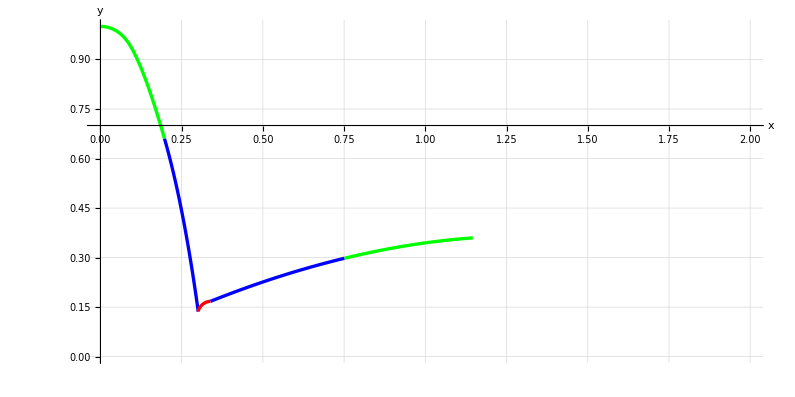

```mathematica
init = {0, 0, 1, l0, 0, 0, 1,0, 0, 0, 0} /. values;

{op1, p1Flight} = flightPhase[init];
{op2, p1Spring2} = spring2Phase[op1];
{op3, p1Stance} = stancePhase[op2];
{op4, p1Spring1} = spring1Phase[op3];
{op5, p2Flight} = flightPhase[op4];
(*
op6 = spring2Phase[op5];
op7 = stancePhase[op6];
op8 = spring1Phase[op7];
*)
Show[p1Flight, p1Spring2, p1Stance, p1Spring1, p2Flight, PlotRange -> {{0, 2}, {0, 1}}]
```